```mathematica
`
```

## Converting input text into a sequence of tokens

When working with text data, we often use a process called tokenization to break down the text into smaller pieces, or tokens.

Once we have our tokens, we need a way to represent them numerically in our machine learning models. To do this, we use a vocabulary that maps each token to a unique integer.

There are various methods of tokenization that we can use, depending on the specific needs of our task. For example, we might use more advanced techniques like Byte-Pair Encoding or WordPiece. However, the underlying principle remains the same. 

Here to construct our small GPT model, we can just tokenize the text into 1-word tokens (OpenAI GPT models use sub-word tokens) along with any accompanying punctuation marks.

### Tokenizing all Shakespeare plays

OpenAI’s GPT models are trained on massive amounts of textual data. For example 60% of GPT-3 pre-training dataset comes from a filtered version of Common Crawl consisting of a total of 410 billion tokens.

For educational purposes, we train our GPT solely on Shakespeare’s plays. Besides having some fun, this allows us to train the model on a single laptop in a reasonable amount of time (around 1 hour).

There are several publicly available repositories containing all Shakespeare’s plays. In order to spare us some time, I’ve shared via the Wolfram Cloud the following list with all lines of Shakespeare’s plays (the file size is around 8MB):

```mathematica
lines=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/jofree/ShakespeareLines"](https://www.wolframcloud.com/obj/jofree/ShakespeareLines)]];
```

We can check a random sample of 5 lines:

```mathematica
RandomSample[lines,5]
```

{"And, like true subjects, sons of your progenitors,","Is it possible?","And this is false you burden me withal.","Day, my lord.","Then honour be but a goal to my will,"}

With Select , StringStartsQ and StringEndsQ we can pick up the proper lines which are written within quotation marks and finally we remove the marks with StringTake:

```mathematica
lines=Select[lines,StringStartsQ[#,"\""]&&StringEndsQ[#,"\""]&];
lines=StringTake[lines,{2,-2}];
```

Once we cleaned up the lines, we can split them into 1-word tokens using StringSplit with WordBoundary:

```mathematica
lines=StringSplit[lines,WordBoundary];
```

We also want to add the end of sentence token “$End”  which can provide context, indicate the model when to stop a sequence and avoiding generating repetitive sequences:

```mathematica
lines=Map[Append[#,"$End"]&,lines];
```

Roughly, Shakespeare wrote a total of ~100k play lines:

```mathematica
Length@lines
```

108755

Let’s check 5 random tokenized sentences:

```mathematica
Column@RandomSample[lines,5]
```

{I, ,could, ,do, ,nothing, ,without, ,bidding,.,$End}
{The, ,one, ,in, ,fear, ,to, ,lose, ,what, ,they, ,enjoy,,,$End}
{To, ,make, ,us, ,wonder,',d, ,at, ,in, ,time, ,to, ,come,.,$End}
{or, ,staggering, ,take, ,this, ,basket, ,on, ,your, ,shoulders,:,$End}
{Brach, ,Merriman,, ,the, ,poor, ,cur, ,is, ,emboss,',d,,,$End}

## Creating the vocabulary

We construct our tokens vocabulary by analyzing the training data and identifying all the distinct words or punctuation characters that appear in the text. We can create the vocabulary by using Union on the list of all tokens:

```mathematica
vocabulary=Union[Flatten[lines]];
```

There are ~30k different tokens:

```mathematica
Length@vocabulary
```

27713

We can compare it with the number of current common English words and we see that both vocabularies are on the same order of magnitude:

```mathematica
Length@WordList[]
```

39176

We can also compare it with the vocabulary used in GPT-2, where ~50k sub-word tokens were used in order to reduce the number of tokens and at the same time allow the model to process all kinds of non-English words and other strange characters from internet:

```mathematica
NetExtract[NetModel["GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"],{"Output","Labels"}]//Short
```

{ t, a,he,in,re,«50248»,$,#,",}

Let’s check some random words from Shakespeare’s plays and see that several of them are much less common nowadays:

```mathematica
RandomSample[vocabulary,15]
```

{borrows,distractions,bescreen,gleeking,spilth,Beginning,priestess,usually,certainly,obstruct,notes,zo,Hero,Iron,nimbleness}

## Tokens Encoder and Decoder

### Encoder

With NetEncoder we determine the integer value of a token based on the vocabulary:

```mathematica
encoder=NetEncoder[{"Class",vocabulary}]
```

NetEncoder[<>]

For example the token “love” corresponds to the following integer:

```mathematica
loveToken=encoder["love"]
```

14382

### Decoder

The output of the model will be a vector with the predicted probabilities for the next token of the sequence. For example the following probabilities vector has 0 probabilities for all tokens with exception of the “love” token that we set to 1 with UnitVector:

```mathematica
vector=UnitVector[Length@vocabulary,loveToken];
```

With NetDecoder we can convert such probabilities vector to the predicted token:

```mathematica
decoder=NetDecoder[{"Class",vocabulary}]
```

NetDecoder[<>]

```mathematica
decoder[vector]
```

love

Choosing the token with the highest probability to make a final prediction is commonly known as greedy decoding or sampling.

## Basic Layers of a GPT Model

GPT models are a type of transformer neural network, the decoder-only transformer. In this section, we will build each type of layer separately and then we will combine them to obtain a final GPT model represented by the following diagram:

-Graphics-

### Tokens and Positional Embedding Layers

#### Tokens embedding

An embedding is a way to represent a token as a vector of numbers. Each token is assigned a unique vector, which is learned by the transformer during training. These embeddings capture the semantic and syntactic relationships between tokens in the text. The dimension of this vector will determine the “width” of the network, which in our small model will be 128, but it can be much larger, like in GPT-3 DaVinci models, 12288.

#### Positional embedding

In addition to token embeddings, transformers also have positional embeddings to encode the position of each token in a sentence. This is important because the order of words in a sentence carries meaning in natural language. In our case, the positional embedding will be learned during training. We could also use a sinusoidal positional embedding like the one used in the original transformer paper (“Attention Is All You Need”, 2017). The results are practically the same.

#### Combining both embeddings

We then add this positional vector to the corresponding token embedding to create a combined representation of the token and its position within the sentence.

```mathematica
embedding[width_, vocabulary_] :=
	NetInitialize @ NetGraph @
		FunctionLayer[
			Module[{emb1, emb2, posembed},
				emb1 = EmbeddingLayer[width][#Input];
				posembed = SequenceIndicesLayer[50][#Input];
				emb2 = EmbeddingLayer[width][posembed];
				emb1 + emb2
			]&
			,
			"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]}
		]
```

We can visualize it as the following NetGraph:

```mathematica
embedding[128, vocabulary]
```

NetGraph[<>]

Now we can represent it with ArrayPlot the initial embeddings for the famous Shakespeare’s sentence “To be, or not to be”. Each row corresponds to a token embedding vector with its added positional embedding:

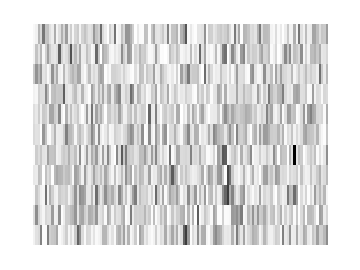

```mathematica
ArrayPlot[embedding[128, vocabulary][{"To"," ","be",","," ","or"," ","not"," ","to","be"}],AspectRatio->0.75]
```

### Masked Multi-head Self-Attention Layer

#### Self-Attention Mechanism

The Self-Attention Mechanism involves generating three matrices called Query, Key and Value. Each of them contain query, key and value vectors for each token in the sequence. We obtain these vectors by multiplying the input sequence embedding by learned weight matrices Wq, Wk and Wv:

Once the query, key, and value vectors have been generated, the Self-Attention Mechanism computes a weight for each token in the sequence by taking the dot product between the query vector for that token and the key vector for every other token in the sequence. The dot products are then scaled by a factor that is the square root of the dimensionality of the key vector.

Next, we apply a softmax function to the scaled dot products to obtain a set of weights that sum to one. These weights are then used to compute a weighted sum of the value vectors, where the weights represent the importance of each token in the sequence.

The resulting weighted sum is then passed through a feedforward neural network to obtain the final output of the Self-Attention Mechanism. This output is then used as input to the next layer of the network.

#### Masked Attention

Masked attention is used to prevent the model from “peeking” at future positions in the input when making predictions for a given position. In masked self-attention, certain positions in the input are “masked” or “blocked” so that the model cannot attend to them when making predictions for a given position. This is typically done by setting the attention weights for these positions to a large negative value, which after the softmax become 0. Basically, the masking prevents the model to see any tokens following the current token it is trying to predict. That’s why sometimes it is also called “Causal Self-Attention”.

#### Attention Heads

The attention heads are a way of parallelizing the Self-Attention Mechanism to allow the model to attend to different parts of the input sequence in a more fine-grained way.

An attention head is essentially a separate instance of the Self-Attention Mechanism that operates in parallel with the other attention heads in the model. Each attention head has its own set of query, key, and value weight matrices, which allows it to focus on different aspects of the input sequence.

By using multiple attention heads, the Transformer model can learn to attend to different parts of the input sequence at the same time, which can improve the quality of the model’s output. For example, one attention head might focus on the syntax of the input sequence, while another attention head might focus on the semantics.

After each attention head has computed its own set of weights, the results are concatenated together before being passed through a linear layer to generate the final output of the Self-Attention Mechanism.

Typically the embedding size is set to be divisible by the number of heads. In our case, the embedding size is 128 and the number of heads will be 4. So the dimension of the key vector will be 32.

#### Dropout Layer

The dropout layer works by randomly setting a fraction of the activations in the previous layer to zero during each training iteration. This has the effect of reducing the capacity of the model and preventing it from relying too heavily on any one feature or set of features.

#### Normalization Layer

The normalization layer is used to normalize the output of the previous layer, which helps to prevent the activations from becoming too large or too small, a phenomenon known as “internal covariate shift”. This normalization is done by centering and scaling the activations to have zero mean and unit variance, respectively.

#### Residual Connection

A residual connection involves adding the input to a layer to the output of that layer before passing it through the next layer of the network. This has the effect of creating a "shortcut" or "skip" connection that allows the gradient to bypass the layer and flow directly to the next layer.

The role of residual connections is to address the problem of vanishing gradients, which can occur in deep neural networks when the gradient signal becomes too small to effectively update the parameters of the model.

#### Masked Self-Attention Block

We can add all the previous layers to create a self-attention block using AttentionLayer, DropoutLayer and NormalizationLayer:

```mathematica
selfAttentionBlock[width_, nheads_] := NetInitialize[
	NetGraph[
		FunctionLayer[
			Module[{keys, queries, values, seq, headWidth=width/nheads;},
			keys = LinearLayer[{nheads, headWidth}] /@ #Input;
			values = LinearLayer[{nheads, headWidth}] /@ #Input;
			queries = LinearLayer[{nheads, headWidth}] /@ #Input;
			queries = queries / Sqrt[headWidth];
			seq = AttentionLayer["Dot", "MultiHead" -> True, "Mask" -> "Causal"][{keys, values, queries}];
			seq = LinearLayer[width] /@ seq;
			seq = DropoutLayer[][seq];
			seq = seq + #Input;
			NormalizationLayer[2 ;; , "Same", "Epsilon" -> 1 / 10^12][seq]
			]&
			,
			"Input" -> {"Varying", width}
		]
	]
]
```

```mathematica
selfAttentionBlock[128, 4]
```

-Graphics-

### Feed-Forward Layer

The Feed-Forward Layer is a fully connected neural network that consists of two linear layers with an activation function in between (GELU ElementwiseLayer function in our case). The first linear layer maps the input to a higher-dimensional space, while the second linear layer maps the output back to the original dimensionality.

The purpose of the Feed-Forward Layer is to introduce non-linearity and allow the model to learn more complex features from the output of the Self-Attention Mechanism. This non-linearity is achieved through the GELU activation function (Gaussian Error Linear Unit), which applies a thresholding function to the output of the first linear layer:

```mathematica
feedForwardBlock[width_] := NetInitialize[
	NetGraph[
		FunctionLayer[
			Module[{seq},
				seq = LinearLayer[4 width] /@ #Input;
				seq = ElementwiseLayer["GELU"][seq];
				seq = LinearLayer[width] /@ seq;
				seq = seq + #Input;
				NormalizationLayer[2 ;; , "Same", "Epsilon" -> 1 / 10^12][seq]
			]&
			,
			"Input" -> {"Varying", width}
		]
	]
]
```

```mathematica
feedForwardBlock[128]
```

-Graphics-

### Decoder-only Transformer

Now, we can put all these layers together to build a decoder-only transformer:

```mathematica
decoderNet[width_, nheads_, blocks_, vocabulary_] := Module[
	{embeddingblock, decoderblock},
	embeddingblock = embedding[width, vocabulary];
	decoderblock = NetFlatten@NetChain[{selfAttentionBlock[width, nheads], feedForwardBlock[width]}];
	NetInitialize@NetGraph@FunctionLayer[
		Module[
			{emb, block},
			emb=embeddingblock[#Input];
			block=decoderblock[emb];
			Table[block=decoderblock[block], blocks-1];
			SoftmaxLayer[]/@LinearLayer[]/@block
		]&,
		"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]},
		"Output"-> {"Varying", NetDecoder[{"Class", vocabulary}]}
	]
]
```

In our case, we build a small GPT model with an embedding size of 128, 4 heads and 4 decoder-blocks:

```mathematica
decoderTransformer=decoderNet[128,4,4,vocabulary]
```

-Graphics-

## Training the GPT model

Finally, we only need to add a cross entropy layer (CrossEntropyLossLayer) as the final layer of the network to calculate the loss between the predicted output and the true output using NetTrain.

The cross-entropy loss is a standard loss function used in many natural language processing tasks, such as language translation, text summarization, and text classification. The loss is calculated by comparing the predicted output to the true output using a probability distribution.

The predicted output is represented as a probability distribution over the vocabulary. The true output, on the other hand, is represented as a one-hot vector with a 1 at the position of the true output word and 0s elsewhere. The cross-entropy loss is calculated by taking the negative logarithm of the predicted probability of the true output word.

The cross-entropy loss is then back-propagated through the network to update the weights of the network in order to minimize the loss. This is done using an optimization algorithm, such as stochastic gradient descent (SGD) or ADAM in our case, which iteratively updates the weights of the network to reduce the loss:

```mathematica
trainingNet=NetGraph@FunctionLayer[
Module[{encode,decode,most,rest},
most=Most[#Input];
rest=Rest[#Input];
decode=decoderTransformer[most];
CrossEntropyLossLayer["Index"][{decode,rest}]]&,
"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]}
]
```

-Graphics-

```mathematica
results=NetTrain[trainingNet,lines,All,MaxTrainingRounds->3,ValidationSet->Scaled[0.1],BatchSize->16]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:18354  rounds:3  time:1.2h  examples/s:67.
data | ,,  training examples:97888  validation examples:10880  processed examples:293664  skipped examples:0
method | ,,  ADAMoptimizer  batch size16CPU
round | ,,  loss:2.98  error:51.0%
validation | ,,  loss:3.  error:50.8%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trainedNet=NetExtract[results["TrainedNet"],"decode"];
```

It’s a good practice to save the trained nets, so if we re-start the session we don’t need to re-train the network again:

```mathematica
CloudPut[trainedNet,"ShakespeareGPT",Permissions->"Public"];
```

Now we can directly obtain the trained net from the cloud using CloudGet:

```mathematica
trainedNet=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/jofree/ShakespeareGPT"](https://www.wolframcloud.com/obj/jofree/ShakespeareGPT)]]
```

NetGraph[<>]

## Autoregressive Text Generation

We can generate full sentences by iteratively getting the next token prediction from our model. At each iteration, we append the predicted token back into the input. This process of predicting a future value (regression), and adding it back into the input (auto) is why you might see a GPT described as autoregressive.

```mathematica
predictor=NetReplacePart[trainedNet,{
{"output", 1}->{SequenceLastLayer[],NetExtract[trainedNet,{"output", 1,"Net"}]},
{"output",2}->NetExtract[trainedNet,{"output", 2,"Net"}],
"Input" -> {"Varying", NetEncoder[{"Class", vocabulary}]},
"Output"->NetDecoder[{"Class", vocabulary}]}
]
```

NetGraph[<>]

A more efficient way to generate text with the trained network would be to unfold the network with NetUnfold in order to avoid computing some parts of the network multiple times. Here, for simplicity we will just use NestWhileList over the predictor:

```mathematica
Column@NestWhileList[Append[#,predictor[#]]&,{"O"},Last[#]!="$End"&,1,20]
```

{O}
{O, }
{O, ,my}
{O, ,my, }
{O, ,my, ,lord}
{O, ,my, ,lord,, }
{O, ,my, ,lord,, ,I}
{O, ,my, ,lord,, ,I, }
{O, ,my, ,lord,, ,I, ,am}
{O, ,my, ,lord,, ,I, ,am, }
{O, ,my, ,lord,, ,I, ,am, ,a}
{O, ,my, ,lord,, ,I, ,am, ,a, }
{O, ,my, ,lord,, ,I, ,am, ,a, ,man}
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, }
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is}
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, }
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, ,a}
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, ,a, }
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, ,a, ,man}
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, ,a, ,man,,}
{O, ,my, ,lord,, ,I, ,am, ,a, ,man, ,is, ,a, ,man,,,$End}

By picking always the token with highest probability (greedy sampling) the model often outputs nonsensical repetitive words. Let’s check some more advanced sampling methods.

### Sampling

We can introduce some stochasticity (randomness) to our generations by sampling from the probability distribution instead of being greedy.

This allows us to generate different sentences given the same input. When combined with techniques like top-k, top-p, and temperature which modify the distribution prior to sampling, the quality of our outputs is greatly increased. These techniques also introduce some hyperparameters that we can play around with to get different generation behaviors (for example, increasing temperature makes our model take more risks and thus be more “creative”):

```mathematica
Column@NestWhileList[Append[#,predictor[#,"RandomSample"->{"Temperature"->.7}]]&,{"O"},Last[#]!="$End"&,1,25]
```

{O}
{O, }
{O, ,my}
{O, ,my, }
{O, ,my, ,dear}
{O, ,my, ,dear, }
{O, ,my, ,dear, ,sweet}
{O, ,my, ,dear, ,sweet, }
{O, ,my, ,dear, ,sweet, ,fellow}
{O, ,my, ,dear, ,sweet, ,fellow,!}
{O, ,my, ,dear, ,sweet, ,fellow,!,$End}

We can also pick up randomly one of the best top 3 tokens each time:

```mathematica
Column@NestWhileList[Append[#,predictor[#,"RandomSample"->{"TopProbabilities"->3}]]&,{"O"},Last[#]!="$End"&,1,25]
```

{O}
{O,, }
{O,, ,what}
{O,, ,what, }
{O,, ,what, ,is}
{O,, ,what, ,is, }
{O,, ,what, ,is, ,the}
{O,, ,what, ,is, ,the, }
{O,, ,what, ,is, ,the, ,matter}
{O,, ,what, ,is, ,the, ,matter, }
{O,, ,what, ,is, ,the, ,matter, ,of}
{O,, ,what, ,is, ,the, ,matter, ,of, }
{O,, ,what, ,is, ,the, ,matter, ,of, ,my}
{O,, ,what, ,is, ,the, ,matter, ,of, ,my, }
{O,, ,what, ,is, ,the, ,matter, ,of, ,my, ,heart}
{O,, ,what, ,is, ,the, ,matter, ,of, ,my, ,heart,?}
{O,, ,what, ,is, ,the, ,matter, ,of, ,my, ,heart,?,$End}

Let’s generate multiple random lines at once. First we need to pick up words from our vocabulary that are starting with an upper case letter:

```mathematica
upperCaseWords=Select[vocabulary,UpperCaseQ[StringTake[#,1]]&& LowerCaseQ[StringDrop[#,1]]&];
```

```mathematica
Length@upperCaseWords
```

6735

```mathematica
RandomSample[upperCaseWords,5]
```

{Please,Damnable,Atlas,Ambassador,Laud}

```mathematica
Column@Table[StringJoin@Most@NestWhile[Append[#,predictor[#,"RandomSample"->{"Temperature"->.7}]]&,RandomSample[upperCaseWords,1],Last[#]!="$End"&,1,25],30]
```

Killingworth and mark the sword of his father on this way
Ban to you.
Tailor of your valour shall be so full of his law
Veiling your word.
William of a very gentleman, I'll have not made the sun, and
Yields you for your pleasure is to behold,
Hard of my life.
Beggar a eager man in a friend of the thought.
Stubborn and our mother: the more of the man that all
Ponton and his own life to thee.
Wink on me, and I do not like, for, to be
Excusez and mocking the great and an new death.
Freely, I will not stay it, my lord, old and I
Maud and the name of the traitor, and I do
Pantheon for this lord.
Muffle the best of your own peace will not seem
Dumb that his majesty and old to be done
Melford and will not be told'd on him.
Dismiss me of the Duke man to be gone.
Chitopher for the way of your intents, I will not quake,
Chi, that you are the people of the law:
Cliffords to my way.
Unready to my grace. I am the beast, you are like my lord
Starr the day of the woman and his life,
Statist I am all but to be glad like her,
Entirely two men, and I am so hot I am a pretty.
Peer after the rage of England of you?
Squire with the worst of thine.
Argus, it were king to you, but I am't that they embrace
Received the earth of this thing is me.

Nice! They  indeed sound like Shakespeare’s lines, but most of them are still nonsensical.

## Further Improvements

Our results aren’t amazing and our trained model won’t write a coherent new Shakespeare’s play. If we want to improve the model here are several things that we could try:

Increase the dimension of the embeddings.

Increase the number of decoder blocks.

Increase the number of heads in the Causal Multi-head Self-Attention.

Increase the length of the training sequences. Putting together multiple lines the model might be able to generate multiple lines that are “coherent”.

Increasing these parameters will also increase the training time of the model. So, we should probably get access to some GPUs.

## Creating a Shakespearean GPT directly using GPT-3

Alternatively, we can create a bot that writes like Shakespeare using a much more powerful GPT model. In this final section, we will use GPT-3 DaVinci model via OpenAI’s API.

### OpenAI API

On the Wolfram Paclet Repository there is a recent paclet called OpenAILink which was created by Christopher Wolfram. To set it up on your session we just need PacletInstall:

```mathematica
PacletInstall["ChristopherWolfram/OpenAILink"]
```

PacletObject[…]

```mathematica
Needs["ChristopherWolfram`OpenAILink`"]
```

Then we need to create a user account on OpenAI and generate your own API key:

```mathematica
SystemCredential["OPENAI_API_KEY"]="your key goes here..."
```

### Writing a Prompt to create a chat bot persona

A prompt is a specific input sequence or set of instructions that is given to a language model to elicit a particular response or output. We can use prompts to guide the behavior of a language model. Our goal is to make chat with characters from Shakespeare’s plays or that writes in his style.

Large Language Models (LLMs) are few shot learners. This means that they can learn new tasks directly from examples of a prompt without the need of re-training or fine-tuning the models.

```mathematica
prompt="Write a fragment of a play that imitates Shakespeare's style. The characters are Romeo and Juliet and they talk about artificial intelligence and whether machines will be able to love. Here there is a fragment of a play from Shakespeare as a reference: ROMEO
[To JULIET] If I profane with my unworthiest hand
This holy shrine, the gentle fine is this:
My lips, two blushing pilgrims, ready stand
To smooth that rough touch with a tender kiss.
JULIET
Good pilgrim, you do wrong your hand too much,
Which mannerly devotion shows in this;
For saints have hands that pilgrims' hands do touch,
And palm to palm is holy palmers' kiss.
ROMEO
Have not saints lips, and holy palmers too?
JULIET
Ay, pilgrim, lips that they must use in prayer.
ROMEO
O, then, dear saint, let lips do what hands do;
They pray, grant thou, lest faith turn to despair.
JULIET
Saints do not move, though grant for prayers' sake.
ROMEO
Then move not, while my prayer's effect I take.
Thus from my lips, by yours, my sin is purged.
JULIET
Then have my lips the sin that they have took.
ROMEO
Sin from thy lips? O trespass sweetly urged!
Give me my sin again.
JULIET
You kiss by the book.
";
```

```mathematica
OpenAICompletion[
			prompt,
			OpenAITemperature -> 0.7,
			OpenAITokenLimit -> 1000
		]
```

ROMEO
What sayest thou of machines and artificial intelligence? Will they be able to love?
JULIET
Alas, I know not. 'Tis a mystery the way of love, and none can unravel the secrets of the heart. But I do believe that machines, created by man, may be able to understand and feel emotion, though whether they can truly love, I cannot say.

And here there is another example generated using the same prompt:

```mathematica
OpenAICompletion[
			prompt,
			OpenAITemperature -> 0.7,
			OpenAITokenLimit -> 2000
		]
```

ROMEO
O Juliet, if machines could love, would they be able to feel the same passion as us?
JULIET
If it is true love, then perhaps they could. For even in the cold of a machine, there is a spark of humanity that can be found. If machines are able to recognize and understand it, then perhaps they could love.

## Useful Resources

The main purpose of this post was to learn about the inner workings of GPT models and transformer neural networks in general. If you are interested in learning more about this topic here are some links that I found useful:

Introduction to Machine Learning by Etienne Bernard, Chapter: Deep Learning Methods.
https://www.wolfram.com/language/introduction-machine-learning/deep-learning-methods/

The Illustrated Transformer: https://jalammar.github.io/illustrated-transformer/

Good review on different Attention Mechanisms: https://lilianweng.github.io/posts/2018-06-24-attention/

The Transformer Family Version 2.0: https://lilianweng.github.io/posts/2023-01-27-the-transformer-family-v2/

## PS: Generating the header image

I created the header image of the post using the same OpenAILink paclet. Dall-e 2 can generate amazing images, it’s just a matter of finding the right prompt and generate a bunch of examples with variations.

I got inspired by looking at prompts that people share on Prompt Hero Hub: https://prompthero.com/

```mathematica
{{-Graphics-, OpenAICreateImage}}["portrait of William Shakespeare next to macro 35mm photo of a robot with a broken heart, like a Mona Lisa on film by david lynch, full of details, matte painting, concept art, smooth, octane render, trending on cgsociety artstation, greg rutkowski, cinematic, hyper realism, high detail, octane render, 8k, iridescent accents, Soft light atmosphere, 8k HDR",ImageSize->Medium]
```

-Graphics-

```mathematica
{{-Graphics-, OpenAICreateImage}}["portrait of William Shakespeare next to macro 35mm photo of a robot with a broken heart, like a Mona Lisa on film by david lynch, full of details, matte painting, concept art, smooth, octane render, trending on cgsociety artstation, greg rutkowski, cinematic, hyper realism, high detail, octane render, 8k, iridescent accents, Soft light atmosphere, 8k HDR",ImageSize->Medium]
```

-Graphics-

```mathematica
{{-Graphics-, OpenAICreateImage}}["portrait of William Shakespeare with half of his head being robot head, bionic, metal, maschine parts, on film by david lynch, full of details, matte painting, concept art, smooth, octane render, trending on cgsociety artstation, greg rutkowski, cinematic, hyper realism, high detail, octane render, 8k, iridescent accents, Soft light atmosphere, 8k HDR",ImageSize->Medium]
```

-Graphics-

```mathematica
{{-Graphics-, OpenAICreateImage}}["portrait of William Shakespeare next to a robot with a broken heart writing a book, like a Mona Lisa on film by david lynch, full of details, matte painting, concept art, smooth, octane render, trending on cgsociety artstation, greg rutkowski, cinematic, hyper realism, high detail, octane render, 8k, iridescent accents, Soft light atmosphere, 8k HDR",ImageSize->Medium]
```

-Graphics-

```mathematica
AttentionLayer
```

```mathematica
Keys@results
```

{data,cos}

```mathematica
Print[{{"Killingworth and mark the sword of his father on this way"}, {"Ban to you."}, {"Tailor of your valour shall be so full of his law"}, {"Veiling your word."}, {"William of a very gentleman, I'll have not made the sun, and"}, {"Yields you for your pleasure is to behold,"}, {"Hard of my life."}, {"Beggar a eager man in a friend of the thought."}, {"Stubborn and our mother: the more of the man that all"}, {"Ponton and his own life to thee."}, {"Wink on me, and I do not like, for, to be"}, {"Excusez and mocking the great and an new death."}, {"Freely, I will not stay it, my lord, old and I"}, {"Maud and the name of the traitor, and I do"}, {"Pantheon for this lord."}}]
```

{{Killingworth and mark the sword of his father on this way},{Ban to you.},{Tailor of your valour shall be so full of his law},{Veiling your word.},{William of a very gentleman, I'll have not made the sun, and},{Yields you for your pleasure is to behold,},{Hard of my life.},{Beggar a eager man in a friend of the thought.},{Stubborn and our mother: the more of the man that all},{Ponton and his own life to thee.},{Wink on me, and I do not like, for, to be},{Excusez and mocking the great and an new death.},{Freely, I will not stay it, my lord, old and I},{Maud and the name of the traitor, and I do},{Pantheon for this lord.}}

```mathematica
{{"Killingworth and mark the sword of his father on this way"}, {"Ban to you."}, {"Tailor of your valour shall be so full of his law"}, {"Veiling your word."}, {"William of a very gentleman, I'll have not made the sun, and"}, {"Yields you for your pleasure is to behold,"}, {"Hard of my life."}, {"Beggar a eager man in a friend of the thought."}, {"Stubborn and our mother: the more of the man that all"}, {"Ponton and his own life to thee."}, {"Wink on me, and I do not like, for, to be"}, {"Excusez and mocking the great and an new death."}, {"Freely, I will not stay it, my lord, old and I"}, {"Maud and the name of the traitor, and I do"}, {"Pantheon for this lord."}}
```

{{Killingworth and mark the sword of his father on this way},{Ban to you.},{Tailor of your valour shall be so full of his law},{Veiling your word.},{William of a very gentleman, I'll have not made the sun, and},{Yields you for your pleasure is to behold,},{Hard of my life.},{Beggar a eager man in a friend of the thought.},{Stubborn and our mother: the more of the man that all},{Ponton and his own life to thee.},{Wink on me, and I do not like, for, to be},{Excusez and mocking the great and an new death.},{Freely, I will not stay it, my lord, old and I},{Maud and the name of the traitor, and I do},{Pantheon for this lord.}}

```mathematica
Print@Flatten[{{"Killingworth and mark the sword of his father on this way"},{"Ban to you."},{"Tailor of your valour shall be so full of his law"},{"Veiling your word."},{"William of a very gentleman, I'll have not made the sun, and"},{"Yields you for your pleasure is to behold,"},{"Hard of my life."},{"Beggar a eager man in a friend of the thought."},{"Stubborn and our mother: the more of the man that all"},{"Ponton and his own life to thee."},{"Wink on me, and I do not like, for, to be"},{"Excusez and mocking the great and an new death."},{"Freely, I will not stay it, my lord, old and I"},{"Maud and the name of the traitor, and I do"},{"Pantheon for this lord."}}]
```

{Killingworth and mark the sword of his father on this way,Ban to you.,Tailor of your valour shall be so full of his law,Veiling your word.,William of a very gentleman, I'll have not made the sun, and,Yields you for your pleasure is to behold,,Hard of my life.,Beggar a eager man in a friend of the thought.,Stubborn and our mother: the more of the man that all,Ponton and his own life to thee.,Wink on me, and I do not like, for, to be,Excusez and mocking the great and an new death.,Freely, I will not stay it, my lord, old and I,Maud and the name of the traitor, and I do,Pantheon for this lord.}

```mathematica
seq =Transpose[{{u,v,w,1,2,3},{x,y,z,4,5,6},{a,b,c,7,8,9}}+{0,0,0}];
Length@seq
seq//MatrixForm
Total[seq,2]//MatrixForm
Transpose[(Transpose[seq]/Total[seq])]//MatrixForm
Total[(seq/seq)][[1]]
```

6

(u | x | a
v | y | b
w | z | c
1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

45+a+b+c+u+v+w+x+y+z

(u/(6+u+v+w) | x/(15+x+y+z) | a/(24+a+b+c)
v/(6+u+v+w) | y/(15+x+y+z) | b/(24+a+b+c)
w/(6+u+v+w) | z/(15+x+y+z) | c/(24+a+b+c)
1/(6+u+v+w) | 4/(15+x+y+z) | 7/(24+a+b+c)
2/(6+u+v+w) | 5/(15+x+y+z) | 8/(24+a+b+c)
3/(6+u+v+w) | 6/(15+x+y+z) | 9/(24+a+b+c))

6

(u+x | v+x | w+x | 1+x | 2+x | 3+x
x+y | 2 y | y+z | 4+y | 5+y | 6+y
a+z | b+z | c+z | 7+z | 8+z | 9+z)

```mathematica
seq//MatrixForm
Total[seq]//MatrixForm
```

(u | x | a
v | y | b
w | z | c
1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

(6+u+v+w
15+x+y+z
24+a+b+c)

```mathematica
seqseq=ArrayReshape[Table[Subscript["a",j],{j, Range@25}],{5,5}];
seqseq//MatrixForm
Total[seqseq,1]//MatrixForm
Total[Transpose[seqseq],1]//MatrixForm
```

(a_1 | a_2 | a_3 | a_4 | a_5
a_6 | a_7 | a_8 | a_9 | a_10
a_11 | a_12 | a_13 | a_14 | a_15
a_16 | a_17 | a_18 | a_19 | a_20
a_21 | a_22 | a_23 | a_24 | a_25)

(a_1+a_6+a_11+a_16+a_21
a_2+a_7+a_12+a_17+a_22
a_3+a_8+a_13+a_18+a_23
a_4+a_9+a_14+a_19+a_24
a_5+a_10+a_15+a_20+a_25)

(a_1+a_2+a_3+a_4+a_5
a_6+a_7+a_8+a_9+a_10
a_11+a_12+a_13+a_14+a_15
a_16+a_17+a_18+a_19+a_20
a_21+a_22+a_23+a_24+a_25)